```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(* Binomial[n,m] ({{n}, {m}}) = (n!)/(m!(n-m)!) *)
```

```mathematica
Binomial[4,1]
```

4

```mathematica
Binomial[4,3]
```

4

```mathematica
Binomial[10,4]
```

210

```mathematica
Binomial[10,6]
```

210

```mathematica
Binomial[4,1]/(Sum[Binomial[4,i],{i,1,4}])
```

4/15

```mathematica
(* prob of getting m H in n flip *)
```

```mathematica
(* ({{n}, {m}})(1/2)^m(1/2)^(n-m) *)
```

```mathematica
Binomial[10,4]*(1/2)^10
```

105/512

```mathematica
N[%]
```

0.205078

```mathematica
Binomial[1000,500]*(1/2)^1000
```

4223253764772446398681479587905863679627375131977316984490513673541022323523784279665820061320349533833790720078461657887534527344541873711717097182804976178494773191621120833690038501245904489755696471267492150071422577902441998133040640534678543005733060259424013478163819189207764154121872206505/167423219872854268898191413915625282900219501828989626163085998182867351738271269139562246689952477832436667643367679191435491450889424069312259024604665231311477621481628609147204290704099549091843034096141351171618467832303105743111961624157454108040174944963852221369694216119572256044331338563584

```mathematica
N[%]
```

0.025225

```mathematica
(* binomial distribution *)
```

```mathematica
(* Success "H" p = 0.5 *)
```

```mathematica
(* Failure "T" p = 0.5 *)
```

```mathematica
(* P(m) = ({{n}, {m}})p^m(1-p)^(n-m) "Binomial Dist" *)
```

```mathematica
PDF[BinomialDistribution[n,p],m]
```

Piecewise[{{(1-p)^(-m+n) p^m Binomial[n,m], 0≤m≤n}, {0, True}}]

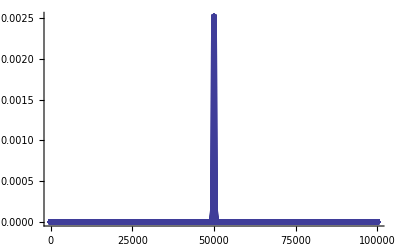

```mathematica
n=100000;p=0.5;
binomialdist=Table[{m,PDF[BinomialDistribution[n,p],m]},{m,0,n}];
ListPlot[binomialdist,PlotStyle->PointSize[0.01],PlotRange->All]
```

```mathematica
sigma=Sqrt[n*p*(1-p)];
```

```mathematica
g[m_]:=(1/Sqrt[2*Pi]*sigma*E^(-(m-n*p)^2/(2*sigma^2)))
```